# Symmetry test

## Initialization and options

```mathematica
Needs["AdvancedMapping`",FileNameJoin[{NotebookDirectory[],"Extra","AdvancedMapping.wl"}]];
Needs["EconomicComputations`",FileNameJoin[{ParentDirectory[NotebookDirectory[]],"EconomicComputations.wl"}]];
```

```mathematica
Middle[l_List]:=Part[l,Floor[Length[l]/2]];

(* Opciones de estilo *)
smallFontSize = 13;
bigFontSize = 15;
plotSize = 500;
colors = {ColorData["Legacy"]["IndianRed"],Black,Blue,ColorData["Legacy"]["Olive"]};

(* Opciones de los procedimientos *)
windowsize = 252;
skip = 20;
resolution = 40;
symmetryPoints = 50;
```

### Package information

```mathematica
?AdvancedMapping`*
```

```mathematica
?EconomicComputations`*
```

## Load database

```mathematica
database = Import[FileNameJoin[{NotebookDirectory[],"DJI_DAX_MXX_NIKKEI_dataset.mx"}]];
AddToDataset[database,"TrendReturns",TrendReturns,{"Prices"}];
AddToDataset[database,"DatedTrendReturns",DatedTrendReturns,{"Dates","Prices"}];
AddToDataset[database,"VelocityTrendReturns",VelocityTrendReturns,{"Prices"}];
AddToDataset[database,"DatedVelocityTrendReturns",DatedVelocityTrendReturns,{"Dates","Prices"}];
```

## Detección de fechas importantes

```mathematica
importantDates = {DateObject[{2001,9,7},"Day","Gregorian",-5.],DateObject[{2008,10,1},"Day","Gregorian",-5.]};
```

```mathematica
importantDatesNames = {"DotCom Crisis","2008 Crisis"};
```

## Intervalos de crisis

```mathematica
dotCom = {DateObject[{2000,3,10}],DateObject[{2002,10,9}]}
```

{Day: Fri 10 Mar 2000,Day: Wed 9 Oct 2002}

```mathematica
bigFuckup = {DateObject[{2007,8,9}],DateObject[{2009,4,2}]}
```

{Day: Thu 9 Aug 2007,Day: Thu 2 Apr 2009}

```mathematica
importantIntervals = {dotCom,bigFuckup}
```

{{Day: Fri 10 Mar 2000,Day: Wed 9 Oct 2002},{Day: Thu 9 Aug 2007,Day: Thu 2 Apr 2009}}

Agregar información a base de datos

```mathematica
rules = {"DotCom Crisis"-> "(a)","2008 Crisis"->"(b)","Brexit"->"(c)","Tequila effect"->"(d)","Japanese asset\nprice bubble"->"(e)"};
```

```mathematica
AddKeyToMarket[database[[1]],"ImportantDates"->{DateObject[{2001,9,7},"Day","Gregorian",-5.],DateObject[{2008,10,1},"Day","Gregorian",-5.],DateObject[{2016,6,23},"Day","Gregorian",-5.]}];
AddKeyToMarket[database[[1]],"ImportantIntervals"->{{DateObject[{2000,3,10},"Day","Gregorian",-5.],DateObject[{2002,10,9},"Day","Gregorian",-5.]},{DateObject[{2007,8,9},"Day","Gregorian",-5.],DateObject[{2009,4,2},"Day","Gregorian",-5.]},{DateObject[{2016,6,23},"Day","Gregorian",-5.],Today}}];
AddKeyToMarket[database[[1]],"ImportantDatesNames"->{"DotCom Crisis","2008 Crisis","Brexit"}/.rules];

AddKeyToMarket[database[[2]],"ImportantDates"->{DateObject[{2001,9,7},"Day","Gregorian",-5.],DateObject[{2008,10,1},"Day","Gregorian",-5.]}];
AddKeyToMarket[database[[2]],"ImportantIntervals"->{{DateObject[{2000,3,10},"Day","Gregorian",-5.],DateObject[{2002,10,9},"Day","Gregorian",-5.]},{DateObject[{2007,8,9},"Day","Gregorian",-5.],DateObject[{2009,4,2},"Day","Gregorian",-5.]}}];
AddKeyToMarket[database[[2]],"ImportantDatesNames"->{"DotCom Crisis","2008 Crisis"}/.rules];

AddKeyToMarket[database[[3]],"ImportantDates"->{DateObject[{1994,12,7},"Day","Gregorian",-6.],DateObject[{2008,10,1},"Day","Gregorian",-5.]}];
AddKeyToMarket[database[[3]],"ImportantIntervals"->{{DateObject[{1994,1,1},"Day","Gregorian",-5.],DateObject[{2001,1,1},"Day","Gregorian",-5.]},{DateObject[{2007,8,9},"Day","Gregorian",-5.],DateObject[{2009,4,2},"Day","Gregorian",-5.]}}];
AddKeyToMarket[database[[3]],"ImportantDatesNames"->{"Tequila effect","2008 Crisis"}/.rules];

AddKeyToMarket[database[[4]],"ImportantDates"->{DateObject[{1992,8,17},"Day","Gregorian",-6.],DateObject[{2008,10,1},"Day","Gregorian",-5.]}];
AddKeyToMarket[database[[4]],"ImportantIntervals"->{{DateObject[{1990,1,1},"Day","Gregorian",-5.],DateObject[{1993,1,1},"Day","Gregorian",-5.]},{DateObject[{2007,8,9},"Day","Gregorian",-5.],DateObject[{2009,4,2},"Day","Gregorian",-5.]}}];
AddKeyToMarket[database[[4]],"ImportantDatesNames"->{"Japanese asset\nprice bubble","2008 Crisis"}/.rules];
```

## Sign ratio

```mathematica
SignRatio[returns_]:= N[Count[Map[Sign,returns],1]/Length[returns]];
SignChangeInTime[market_,window_]:=Block[{part,ratios},
part = Partition[market["DatedReturns"],window,1];
ratios = Map[{Last[#[[All,1]]],SignRatio[#[[All,2]]]}&,part];
Return[ratios];
];
```

```mathematica
ratioData = Map[SignChangeInTime[#,500]&,database];
```

```mathematica
SignRatioPlot[database_,window_]:=Block[{ratioData},
ratioData = Map[SignChangeInTime[#,window]&,database];
DateListPlot[
ratioData,
PlotLegends->Placed[LineLegend[database[[All,"Name"]],LegendFunction->(Framed[#,Background->Opacity[0.6,White]]&)],{Right,Bottom}],
PlotTheme->"Monochrome", 
FrameLabel->{Style["Date",15], Style["Ratio",15]}, 
ImageSize->plotSize,
GridLines->{{},{0.5}},
PlotLabel->"Ratio Upward/Total price signs",
PlotMarkers->None,
Joined->True,
PlotRange->{Automatic,{0.2,0.7}},

BaseStyle->FontSize->smallFontSize,
GridLinesStyle->{Directive[Black,Thick,Dashed],Directive[Thin,Black]},
PlotStyle->colors
]
];
```

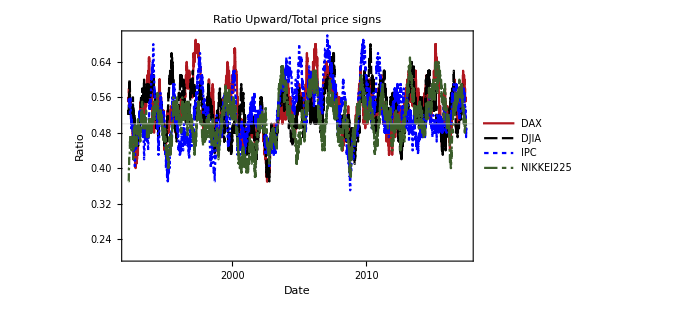
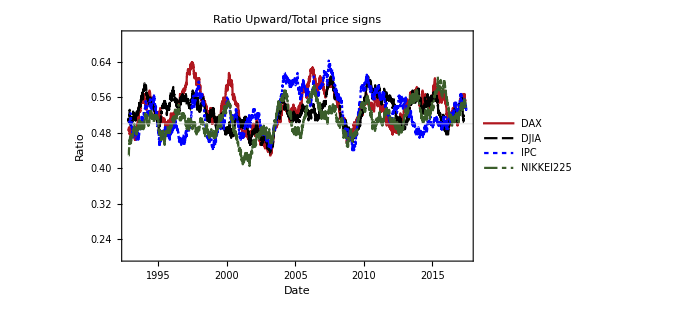
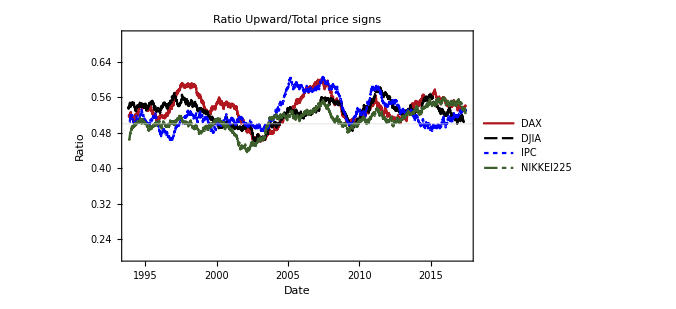

```mathematica
Map[SignRatioPlot[database,#]&,{100,252,500}]
```

## Symmetry analysis

```mathematica
UpperPercentagePointLine[cmin_,cmax_,cl_]:= {{cmin, UpperPercentagePoint[cl]},{cmax,UpperPercentagePoint[cl]}};

PlotSymmetry[market_,returnType_]:= Module[{returns,standardError,tn,upperLineLimit,meanline,cMax,cMin,cFill,cline,upp,plotData,p},
returns = market[returnType];
standardError = StandardDeviation[returns] / Sqrt[Length[returns]];
tn = MeasureTn[returns];
upperLineLimit = Max[tn["TnValues"][[All,2]]];

(* Plot lines *)
meanline=Line[{{Mean[returns],0},{Mean[returns],upperLineLimit/2.5}}];

cMin = Line[{{tn["PlausibleSymmMin"],0},{tn["PlausibleSymmMin"],upperLineLimit/2.5}}];
cMax = Line[{{tn["PlausibleSymmMax"],0},{tn["PlausibleSymmMax"],upperLineLimit/2.5}}];
cFill = Rectangle[{tn["PlausibleSymmMin"],0},{tn["PlausibleSymmMax"],upperLineLimit/2.5}];

cline = Line[{{MinimalBy[tn["TnValues"],Last][[1,1]],0},{MinimalBy[tn["TnValues"],Last][[1,1]],upperLineLimit/2.5}}];
upp = Map[UpperPercentagePointLine[tn["MinimumC"],tn["MaximumC"],#]&,{0.01,0.05,0.1}];
plotData = Join[{tn["TnValues"]},upp];

p = ListLinePlot[plotData,
PlotTheme->"Monochrome",
FrameLabel->{
Style["c",bigFontSize],
Style["T_n(c)",bigFontSize]
},
Epilog->{
meanline,
cline,
cMin,
cMax,

{
Gray,
Opacity[0.4],
cFill
},

Inset[Text["μ"],{Mean[returns],upperLineLimit/2}],
Inset[Text["C_Max"],{tn["PlausibleSymmMax"],upperLineLimit/2}],
Inset[Text["C_Min"],{tn["PlausibleSymmMin"],upperLineLimit/2}],
Inset[Text["C"],{MinimalBy[tn["TnValues"],Last][[1,1]],1.7+upperLineLimit/2}]
},
PlotLegends->Placed[{"T_n","99% CL","95% CL","90% CL"},{Right,Top}], 
PlotLabel->market["Name"],ImageSize->plotSize,Frame->True,BaseStyle->FontSize->smallFontSize,
TicksStyle->Large,PlotMarkers->None, PlotStyle->colors
];
Return[p];
];
```

## Best symmetry point

```mathematica
CInTime[market_,datedreturnType_,windowsize_,skip_:1]:=Module[{parts,partTr,CList},
parts = Partition[market[datedreturnType], windowsize,skip];
CList =ProgressMap[
{Last[#[[All,1]]],MeasureTn[ #[[All,2] ]]["BestSymmetry"]}&,
parts,
"Label"->StringJoin["Calculating C in time for ",market["Name"]]
];
Return[CList];
];

μInTime[market_,datedreturnType_,windowsize_,skip_:1]:=Module[{parts,partTr,CList},
parts = Partition[market[datedreturnType], windowsize,skip];
CList =ProgressMap[{Last[#[[All,1]]],Mean[#[[All,2]]]}&,parts];
Return[CList];
];

PlotCInTime[database_,returnFunction_,windowsize_,skip_]:=Block[{actualReturnType,plotData,p},
plotData = Map[CInTime[#,returnFunction,windowsize,skip]&,database];

p = DateListPlot[plotData,
PlotTheme->"Monochrome",
FrameLabel->{Style["Date",bigFontSize], Style["C",bigFontSize]}, 
ImageSize->plotSize,
PlotLegends->database[[All,"Name"]],
BaseStyle->FontSize->smallFontSize,
GridLines->{importantDates,{0}},
GridLinesStyle->{Directive[Black,Thick,Dashed],Directive[Thin,Black]},
PlotMarkers->None,
PlotStyle->colors
];
Return[p];
];
```

¿Qué ocurre en las fechas de crisis?

```mathematica
ClosestDate[list_,date_]:=First[MinimalBy[list,Abs[QuantityMagnitude[DateDifference[First[#],date]]]&]];
MakeDateInverval[{first_,last_},{min_,max_}]:=Block[{cMin, cMax, cFill},
cMin = Line[{{first,min-10*Abs[min]},{first,max+10*Abs[max]}}];
cMax = Line[{{last,min-10*Abs[min]},{last,max+10*Abs[max]}}];
cFill = {Opacity[0.3],Rectangle[{first,min-10*Abs[min]},{last,max+10*Abs[max]}]};
{cMin,cMax,cFill}
];

PlotCInTimeInCrisis[market_,returnFunction_,windowSize_:252,skip_:40]:=Block[{plotData,p,crashLabels},
plotData = CInTime[market,returnFunction,windowSize,skip];
crashLabels = MapThread[
Callout[
ClosestDate[plotData,#1],#2,Above,
LeaderSize->35,CalloutStyle->Directive[Black,Thick],Appearance->"SlantedLabel"
]&,
{market["ImportantIntervals"][[All,1]],market["ImportantDatesNames"]}
];

p = DateListPlot[
{plotData,crashLabels},
PlotTheme->"Monochrome",
FrameLabel->{Style["Date",bigFontSize], "C"}, 

ImageSize->plotSize,
BaseStyle->FontSize->smallFontSize,
GridLinesStyle->{Directive[Black,Thick,Dashed],Directive[Thin,Black]},
PlotMarkers->None,
PlotRange->{{DateObject[{1989,1,1}],DateObject[{2018,9,24},"Day","Gregorian",-5.]},All},
PlotRangePadding->Automatic,
GridLines->{{},{0}},
Joined->{True,False},
PlotStyle->newColors,
PlotLabel->market["Name"]
];
Return[p];
]
```

Simple returns

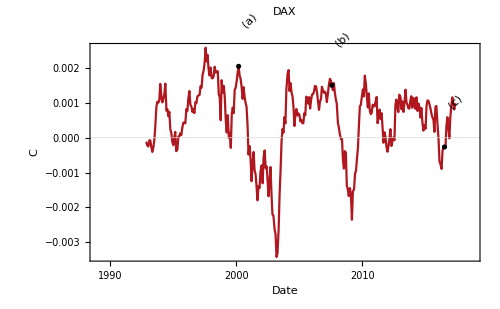
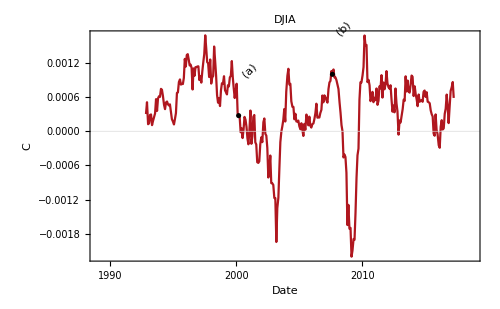
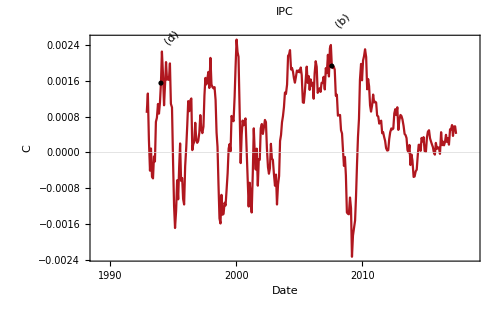
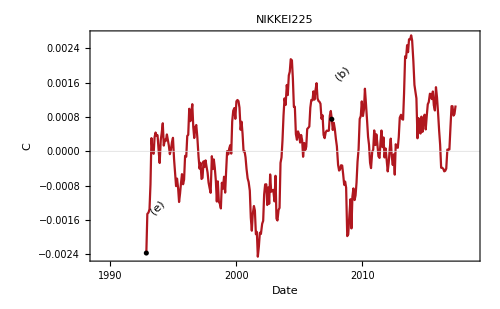

```mathematica
Map[PlotCInTimeInCrisis[#,"DatedReturns",windowsize,skip]&,database]
```

Trend returns

Compensa el tamaño de la ventana para que aun así represente 252 trading days.

```mathematica
TRScaleCompensate[n_,market_]:=n/Round[Mean[TrendDuration[market["Prices"]]]];
```

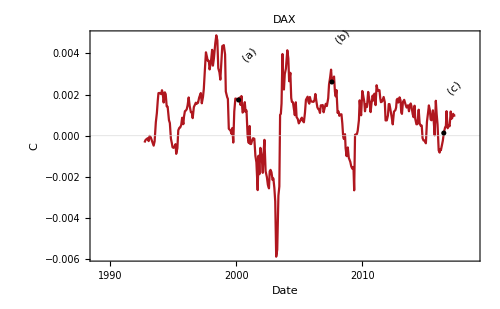
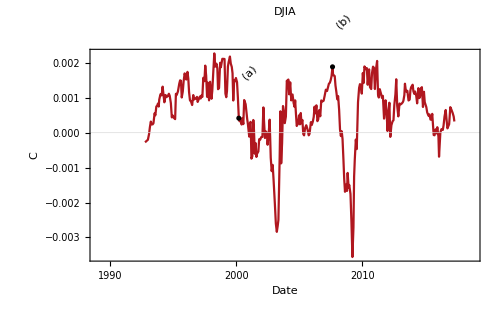
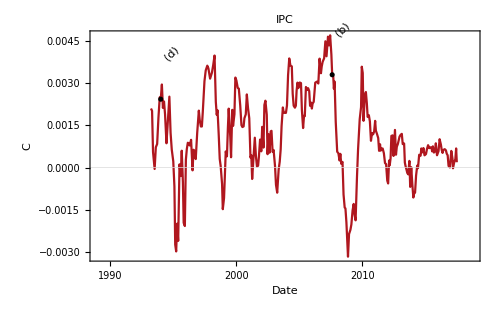
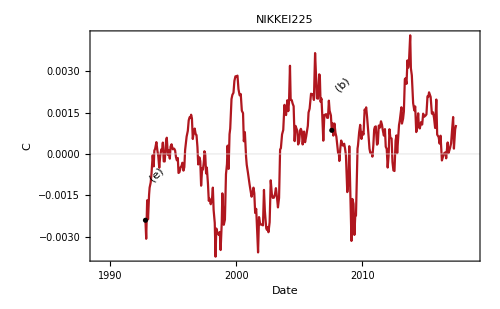

```mathematica
Map[PlotCInTimeInCrisis[#,"DatedTrendReturns",TRScaleCompensate[windowsize,#],TRScaleCompensate[skip,#]]&,database]
```

Velocities

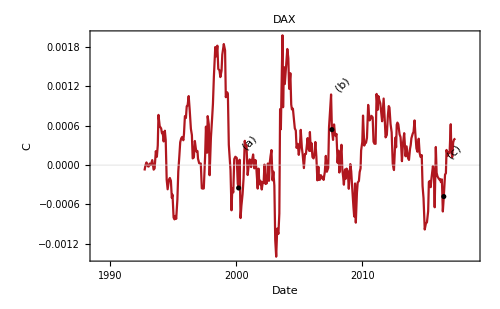
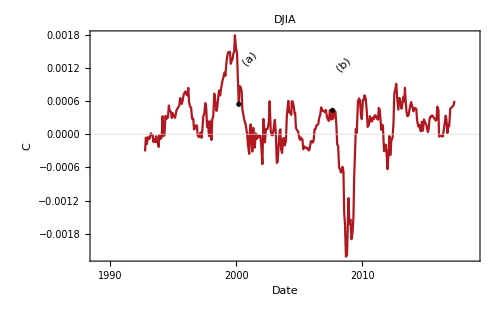
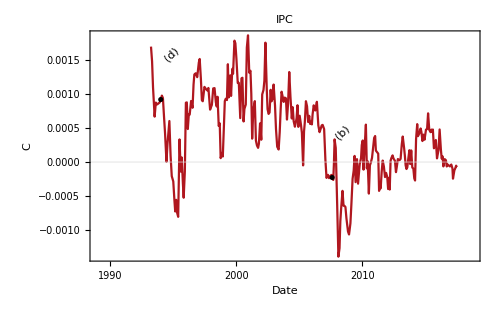
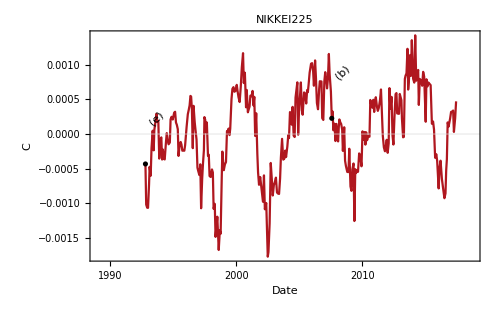

```mathematica
Map[PlotCInTimeInCrisis[#,"DatedVelocityTrendReturns",TRScaleCompensate[windowsize,#],TRScaleCompensate[skip,#]]&,database]
```

## Symmetry around C

```mathematica
TnCInTime[market_,datedreturnType_,windowsize_,skip_:1]:=Block[{parts,CList},
parts = Partition[market[datedreturnType], windowsize,skip];
CList = Map[{Last[#[[All,1]]],MeasureTn[#[[All,2]], 0.05]["Tn(C)"]}&,parts];
Return[CList];
];
PlotTnCInTimeInCrisis[market_,returnFunction_,windowSize_:252,skip_:40]:=Block[{plotData,uppList,actualReturnType,p,crashLabels,firstDate,lastDate,legends},
plotData =TnCInTime[market,returnFunction,windowSize,skip];
crashLabels = MapThread[
Callout[
ClosestDate[plotData,#1],#2,Above,
LeaderSize->35,CalloutStyle->Directive[Black,Thick],Appearance->"SlantedLabel"
]&,
{market["ImportantIntervals"][[All,1]],market["ImportantDatesNames"]}
];

firstDate = DateObject[{1989,1,1}];
lastDate = DateObject[{2018,9,24},"Day","Gregorian",-5.];

uppList = Map[{{firstDate, UpperPercentagePoint[#]},{lastDate,UpperPercentagePoint[#]}}&,{0.01,0.05,0.1}];
legends = {Style["T_n(c = C)",bigFontSize],Style["99% CL",bigFontSize],Style["95% CL",bigFontSize],Style["90% CL",bigFontSize]};

p = DateListPlot[
Append[Join[{plotData},uppList],crashLabels],
PlotTheme->"Monochrome",
FrameLabel->{Style["Date",bigFontSize], Style["T_n-value",bigFontSize]}, 
ImageSize->plotSize,
BaseStyle->FontSize->smallFontSize,
GridLinesStyle->{Directive[Black,Thick,Dashed],Directive[Thin,Black]},
PlotLegends->Placed[LineLegend[legends,LegendFunction->(Framed[#,Background->Opacity[0.6,White]]&)],{Left,Top}],
PlotMarkers->None,
PlotRange->{{firstDate,lastDate},All},
PlotRangePadding->Automatic,
Joined->{True,True,True,True,False},
PlotStyle->newColors,
PlotLabel->market["Name"]
];
Return[p];
]
```

Simple returns

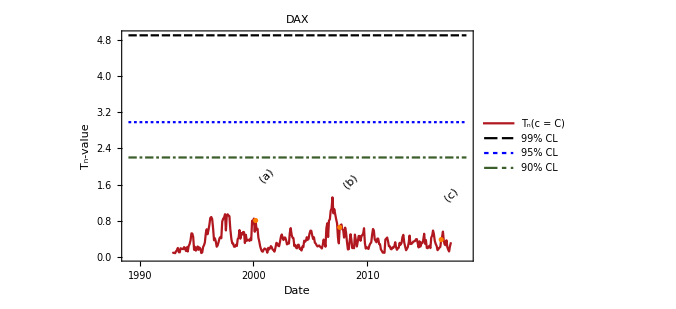
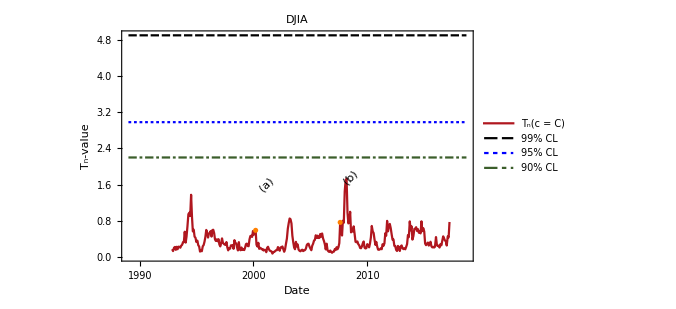
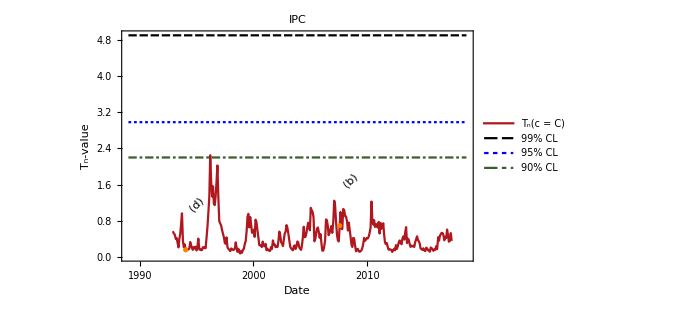
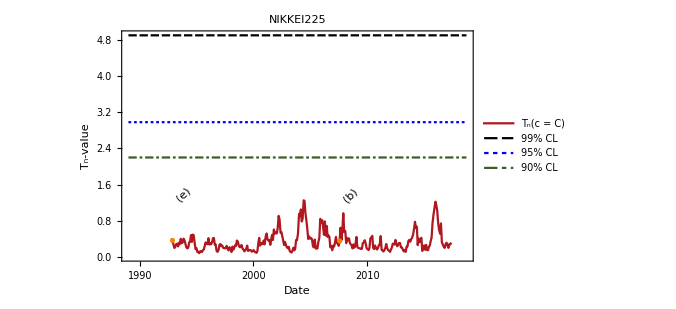

```mathematica
Map[PlotTnCInTimeInCrisis[#,"DatedReturns",windowsize,skip]&,database]
```

Trend returns

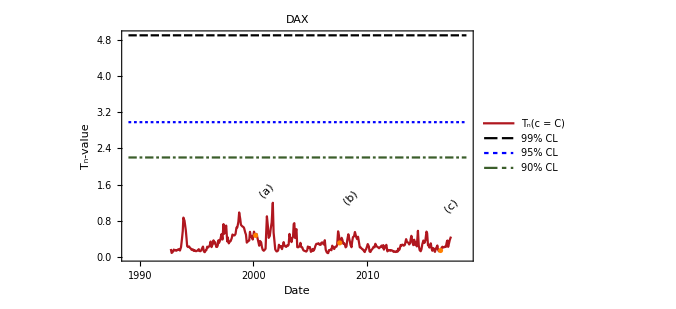
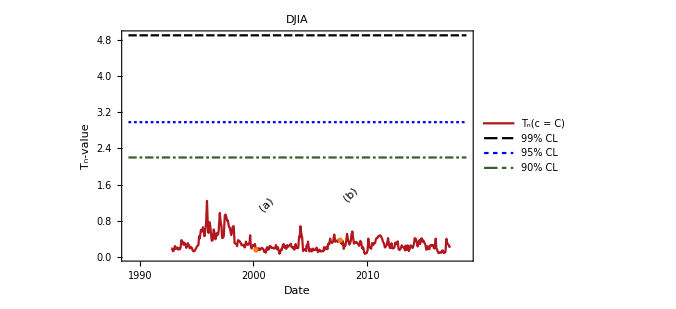
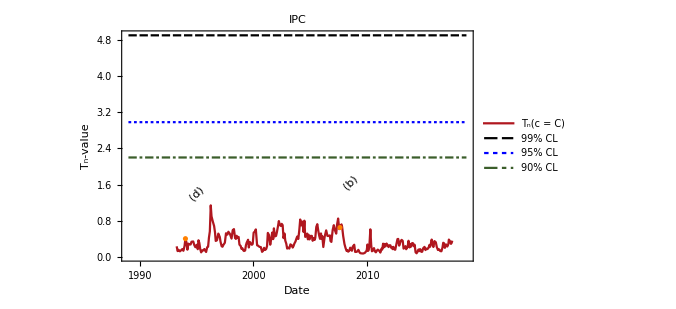
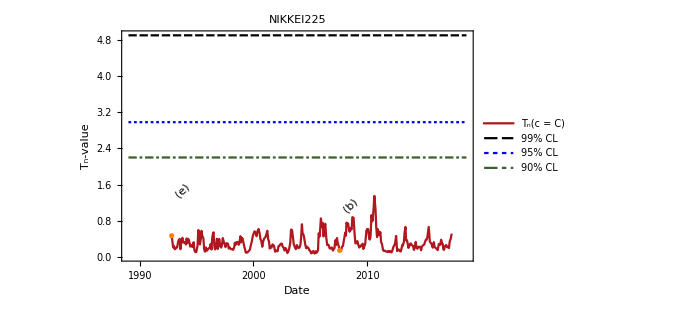

```mathematica
Map[PlotTnCInTimeInCrisis[#,"DatedTrendReturns",TRScaleCompensate[windowsize,#],TRScaleCompensate[skip,#]]&,database]
```

Velocities

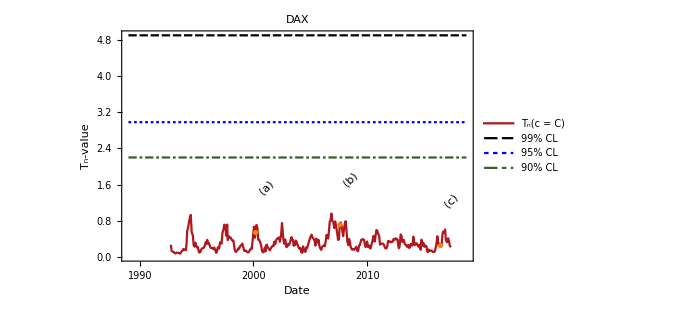
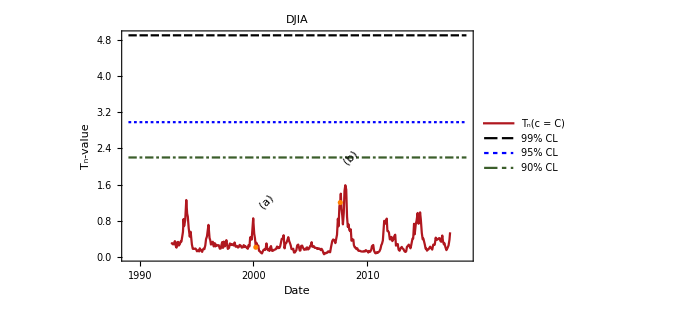
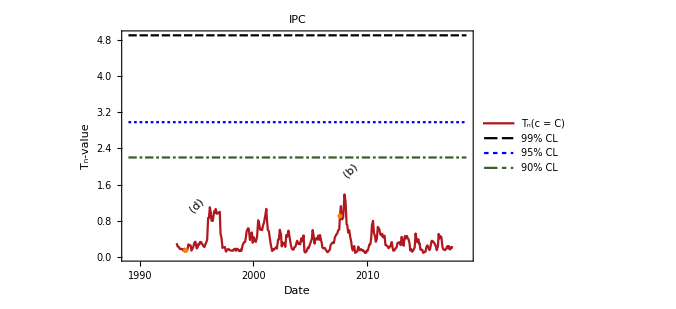
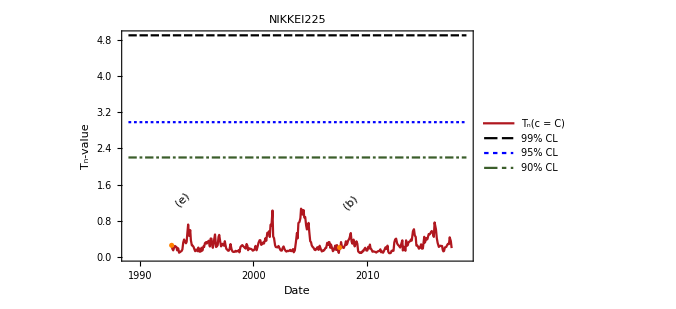

```mathematica
Map[PlotTnCInTimeInCrisis[#,"DatedVelocityTrendReturns",TRScaleCompensate[windowsize,#],TRScaleCompensate[skip,#]]&,database]
```

## Simmetry around c = 0

```mathematica
TnZeroInTime[market_,datedreturnType_,windowsize_,skip_:1]:=Block[{parts,CList},
parts = Partition[market[datedreturnType], windowsize,skip];
CList = Map[{Last[#[[All,1]]],Tn[N[#[[All,2]]],0.0]}&,parts];
Return[CList];
];

newColors = Join[colors,{Orange,Purple,Brown}];
PlotTnZeroTime[database_,returnFunction_,windowsize_,skip_]:=Block[{plotData,p,firstDate,lastDate,uppList,legends},
plotData =ProgressParallelMap[TnZeroInTime[#,returnFunction,windowsize,skip]&,database];

firstDate = Min[Map[First[First[#]]&,plotData]];
lastDate = Max[Map[First[Last[#]]&,plotData]];

uppList = Map[{{firstDate, UpperPercentagePoint[#]},{lastDate,UpperPercentagePoint[#]}}&,{0.01,0.05,0.1}];
legends = Join[database[[All,"Name"]],{Style["99% CL",bigFontSize],Style["95% CL",bigFontSize],Style["90% CL",bigFontSize]}];

p = DateListPlot[
Join[plotData,uppList],
PlotTheme->"Monochrome",
FrameLabel->{Style["Date",bigFontSize], Style["T_n(c = 0)",bigFontSize]}, 
ImageSize->plotSize,
PlotLegends->legends,
BaseStyle->FontSize->smallFontSize,
GridLines->{importantDates,{}},
GridLinesStyle->Directive[Black,Thick,Dashed],
PlotMarkers->None,
PlotStyle->newColors,
PlotRange->Full
];
Return[p];
];
```

Fechas de crisis

```mathematica
PlotTnZeroInTimeInCrisis[market_,returnFunction_,windowSize_:252,skip_:40]:=Block[{plotData,actualReturnType,p,crashLabels,uppList,firstDate,lastDate,legends},
plotData =TnZeroInTime[market,returnFunction,windowSize,skip];
crashLabels = MapThread[
Callout[
ClosestDate[plotData,#1],#2,Above,
LeaderSize->35,CalloutStyle->Directive[Black,Thick],Appearance->"SlantedLabel"
]&,
{market["ImportantDates"],market["ImportantDatesNames"]}
];

firstDate = DateObject[{1989,1,1}];
lastDate = DateObject[{2018,9,24},"Day","Gregorian",-5.];

uppList = Map[{{firstDate, UpperPercentagePoint[#]},{lastDate,UpperPercentagePoint[#]}}&,{0.01,0.05,0.1}];
legends = {Style["T_n(c = 0)",bigFontSize],Style["99% CL",bigFontSize],Style["95% CL",bigFontSize],Style["90% CL",bigFontSize]};

p = DateListPlot[
Append[Join[{plotData},uppList],crashLabels],
PlotTheme->"Monochrome",
FrameLabel->{Style["Date",bigFontSize], Style["T_n-value",bigFontSize]},
ImageSize->plotSize,
BaseStyle->FontSize->smallFontSize,
GridLinesStyle->{Directive[Black,Thick,Dashed],Directive[Thin,Black]},
PlotLegends->Placed[LineLegend[legends,LegendFunction->(Framed[#,Background->Opacity[0.6,White]]&)],{Left,Top}],
PlotMarkers->None,
PlotRange->{{firstDate,lastDate},All},
PlotRangePadding->Automatic,
Joined->{True,True,True,True,False},
PlotStyle->newColors,
PlotLabel->market["Name"]
];
Return[p];
]
```

Simple returns

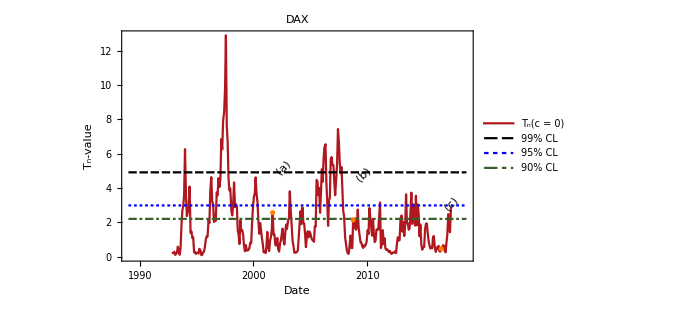
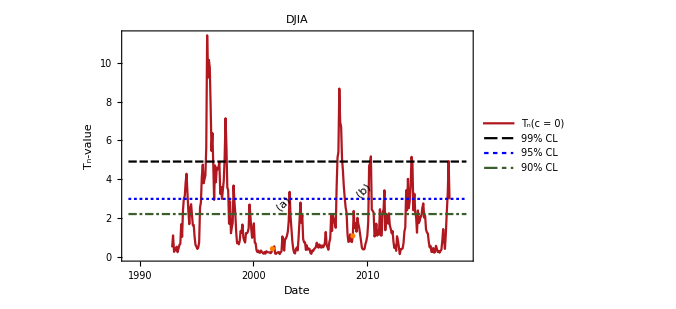
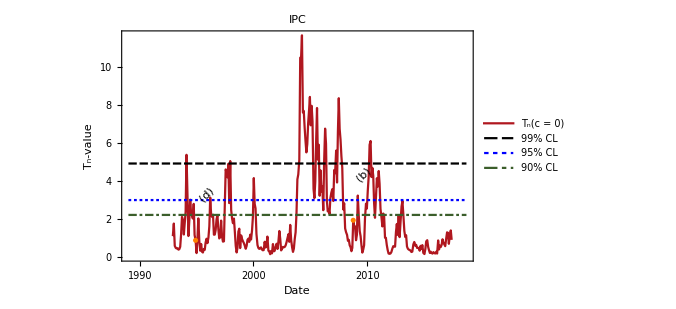
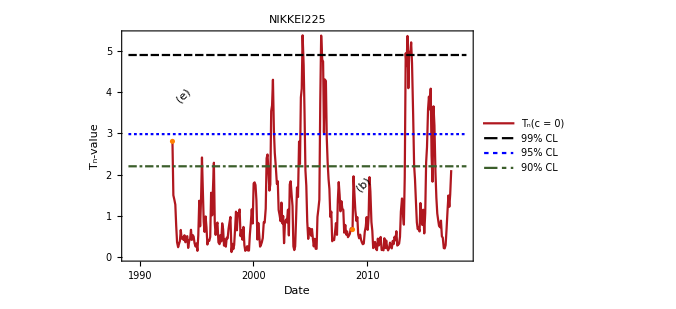

```mathematica
Map[PlotTnZeroInTimeInCrisis[#,"DatedReturns",windowsize,skip]&,database]
```

Trend returns

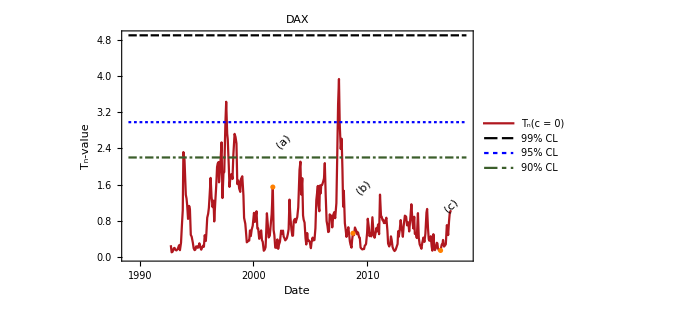
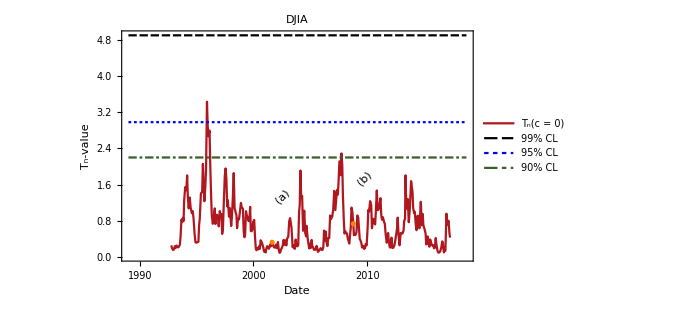
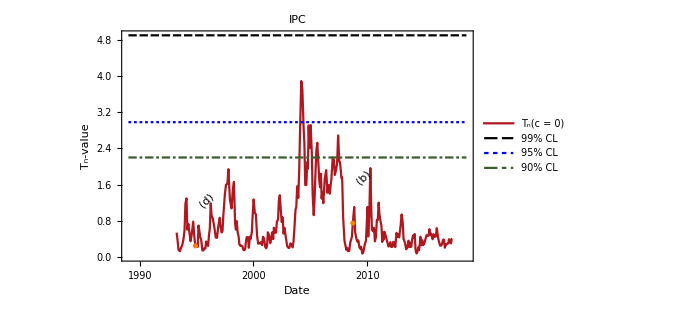
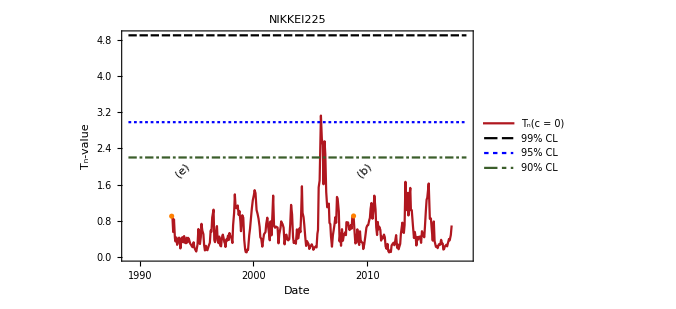

```mathematica
Map[PlotTnZeroInTimeInCrisis[#,"DatedTrendReturns",TRScaleCompensate[windowsize,#],TRScaleCompensate[skip,#]]&,database]
```

Velocities trend returns

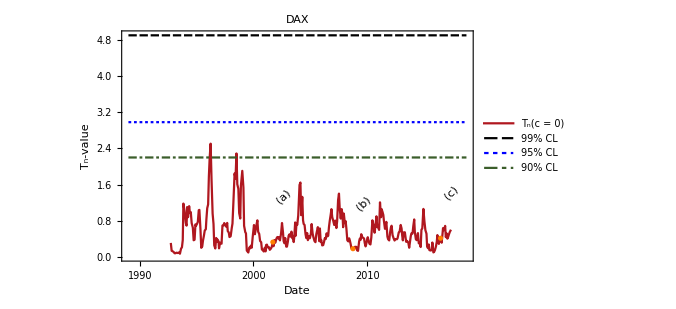
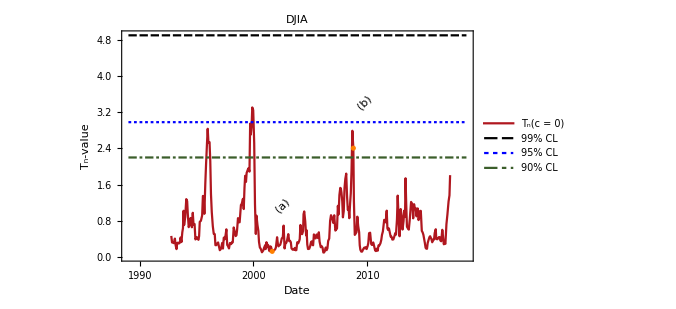
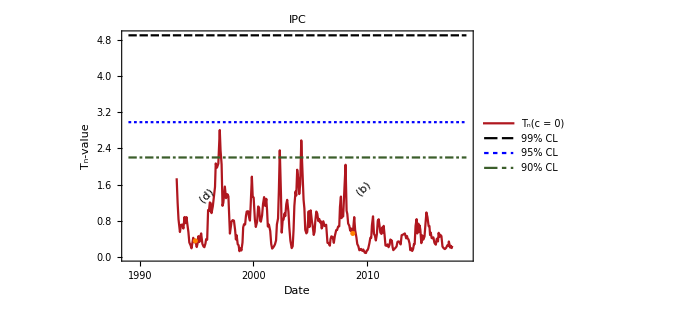
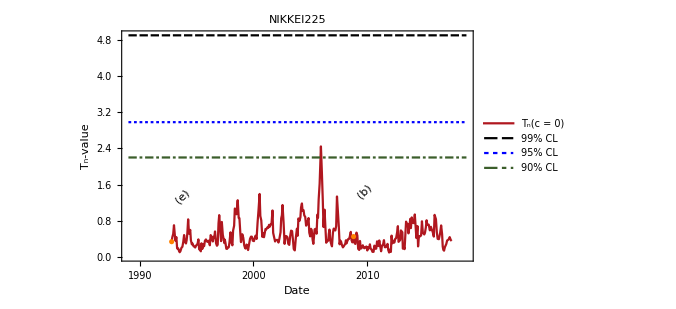

```mathematica
Map[PlotTnZeroInTimeInCrisis[#,"DatedVelocityTrendReturns",TRScaleCompensate[windowsize,#],TRScaleCompensate[skip,#]]&,database]
```

## Symmetry interval

```mathematica
ClosestDate[list_,date_]:=First[MinimalBy[list,Abs[QuantityMagnitude[DateDifference[First[#],date]]]&]];
SymmetryTestInTime[market_,datedreturnType_,CL_,windowsize_,skip_:1]:=Module[{parts,partTr,symTest,plotPoints,means},
parts = Partition[market[datedreturnType], windowsize,skip];
symTest =ProgressParallelMap[
{Middle[#[[All,1]]],MeasureTn[#[[All,2]],CL]}&,
parts,
"Label"->StringJoin["Calculating symmetry interval in time for ",market["Name"]],
Method->"CoarsestGrained"
];
Return[symTest];
];
PlotSymmetryIntervalInTime[market_,returnFunction_,CL_,windowsize_,skip_:1]:=Block[{test,dates,testResults,bestSymmData,crashLabels,legend},
test = SymmetryTestInTime[market,returnFunction,CL,windowsize,skip];
dates = test[[All,1]];
testResults = test[[All,2]];
bestSymmData = Thread[{dates,testResults[[All,"BestSymmetry"]]}];


If[market["Name"] == "DJIA",
legend = Placed[LineLegend[{"C","C_min","C_max"},LegendFunction->(Framed[#,Background->Opacity[0.6,White]]&),LabelStyle->11],{Right,Bottom}];
,
legend = None
];

DateListPlot[
{
Thread[{dates,testResults[[All,"BestSymmetry"]]}],
Thread[{dates,testResults[[All,"PlausibleSymmMin"]]}],
Thread[{dates,testResults[[All,"PlausibleSymmMax"]]}]
}
,
PlotTheme->"Monochrome",
FrameLabel->{Style["Date",bigFontSize], Style["c",bigFontSize]}, ImageSize->plotSize,
PlotLegends->legend,
BaseStyle->FontSize->smallFontSize,
GridLines->{{},{0}},
GridLinesStyle->{Directive[Black,Thick,Dashed],Directive[Thin,Black]},
PlotMarkers->None,
Joined->{True,True,True,False},
PlotStyle->{RGBColor[0., 0.21, 0.52],RGBColor[0., 0.54, 0.51],RGBColor[0, 0, 1],RGBColor[0.230003, 0.370006, 0.170003],RGBColor[1, 0.5, 0],RGBColor[0.5, 0, 0.5],RGBColor[0.6, 0.4, 0.2]},
Filling->{2->{3}},
PlotLabel->market["Name"],
PlotRange->All,
PlotRangePadding->Automatic
]
];
```

Simple returns

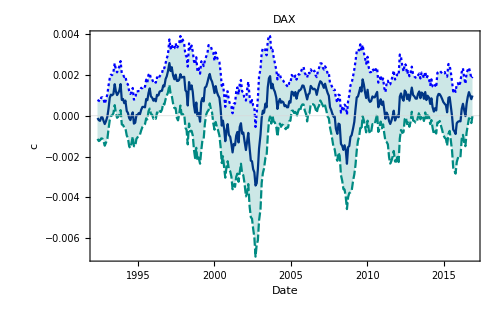
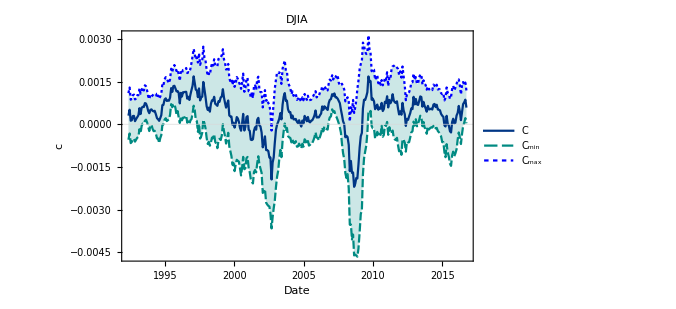
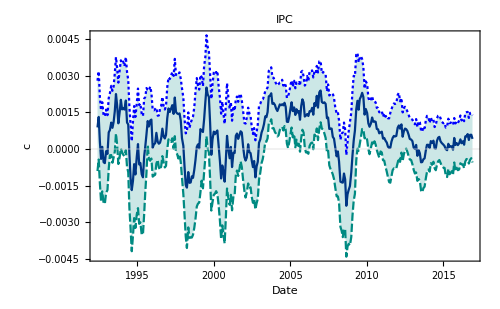
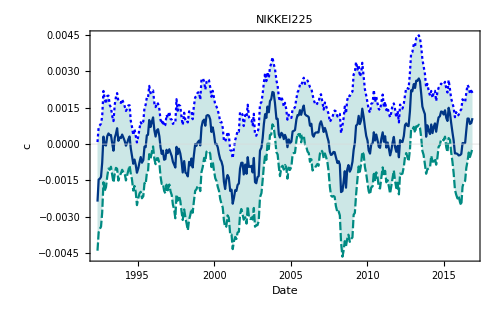

```mathematica
Map[PlotSymmetryIntervalInTime[#,"DatedReturns",0.05,windowsize,skip]&,database]
```

Trend returns

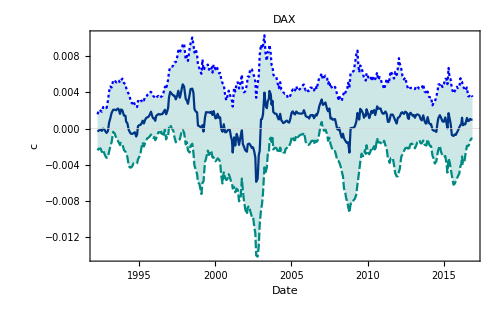
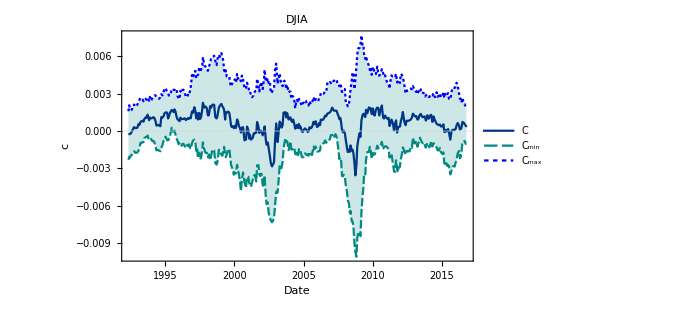
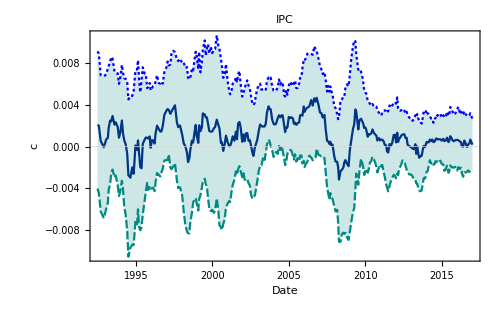
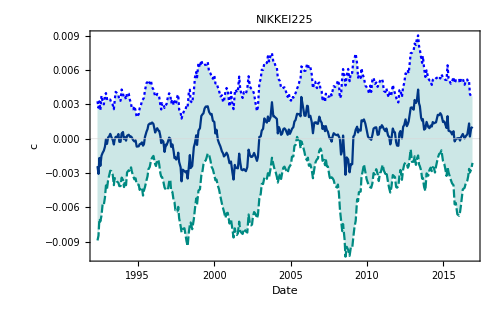

```mathematica
Map[PlotSymmetryIntervalInTime[#,"DatedTrendReturns",0.05,TRScaleCompensate[windowsize,#],TRScaleCompensate[skip,#]]&,database]
```

Velocity trend return

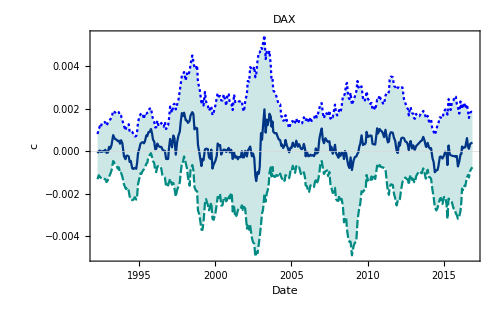
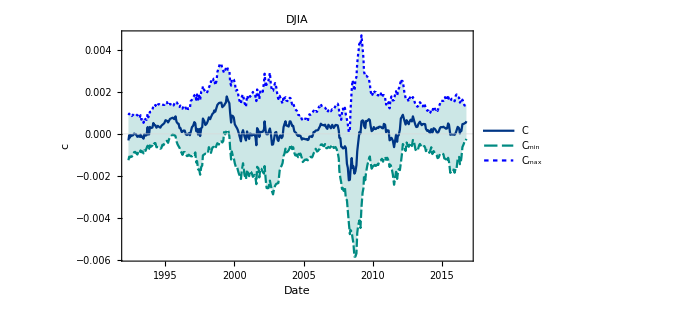
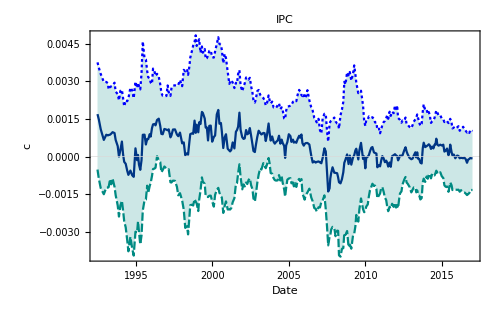
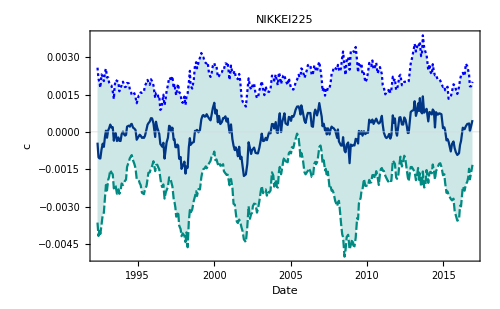

```mathematica
Map[PlotSymmetryIntervalInTime[#,"DatedVelocityTrendReturns",0.05,TRScaleCompensate[windowsize,#],TRScaleCompensate[skip,#]]&,database]
```